Analiza danych z qc

```mathematica
path = "/Users/jakub/Developer/qc/qc/files/";
outNames = FileNames["*", path<>"outputs"];
files = Table[Flatten@Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
{length, visibility} = Transpose@ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
data =Table[{length[[i]], visibility[[i]], files[[i]]}, {i, 1, Length@length}];
means = Table[{length[[i]], visibility[[i]], Mean[files[[i]]]},{i,1,Length@length}];
```

```mathematica
ByLength=Gather[means, First[#1]==First[#2]&]
```

{{{1,0.35,5.73581×10^-17},{1,0.4,6.13985×10^-17},{1,0.45,1.00431×10^-16},{1,0.5,1.33344×10^-16},{1,0.55,1.14806×10^-16},{1,0.6,3.35963×10^-16},{1,0.65,1.73968×10^-16},{1,0.7,1.33489×10^-16},{1,0.75,8.42605×10^-17},{1,0.8,9.42227×10^-17},{1,0.85,1.07756×10^-16},{1,0.9,1.99798×10^-16},{1,0.95,2.16023×10^-16},{1,1.,1.31062×10^-16}},{{2,0.35,0.0376132},{2,0.4,0.0320101},{2,0.45,0.0599541},{2,0.5,0.0562922},{2,0.55,0.0794907},{2,0.6,0.100724},{2,0.65,0.104396},{2,0.7,0.146203},{2,0.75,0.137334},{2,0.8,0.146024},{2,0.85,0.173097},{2,0.9,0.180077},{2,0.95,0.19272},{2,1.,0.236549}},{{3,0.35,0.0475167},{3,0.4,0.0465391},{3,0.45,0.0881264},{3,0.5,0.100149},{3,0.55,0.137735},{3,0.6,0.177527},{3,0.65,0.205544},{3,0.7,0.267841},{3,0.75,0.30211},{3,0.8,0.349888},{3,0.85,0.406928},{3,0.9,0.47064},{3,0.95,0.537939},{3,1.,0.685371}},{{4,0.35,0.0475167},{4,0.4,0.0465391},{4,0.45,0.0881264},{4,0.5,0.100149},{4,0.55,0.137897},{4,0.6,0.178688},{4,0.65,0.210609},{4,0.7,0.277186},{4,0.75,0.320665},{4,0.8,0.383581},{4,0.85,0.452484},{4,0.9,0.557996},{4,0.95,0.66724},{4,1.,0.797608}},{{5,0.75,0.287481},{5,0.8,0.321549},{5,0.85,0.460107},{5,0.95,0.704564},{5,1.,0.85211}},{{6,0.8,0.394696},{6,0.85,0.463479},{6,0.9,0.582342},{6,0.95,0.706977},{6,1.,0.899598}},{{7,0.8,0.373194},{7,0.85,0.449898},{7,0.9,0.575325},{7,0.95,0.694066},{7,1.,0.920931}}}

```mathematica
Table[Last@Transpose[ByLength[[i]]], {i, 1, Length@ByLength}]
```

{{5.73581×10^-17,6.13985×10^-17,1.00431×10^-16,1.33344×10^-16,1.14806×10^-16,3.35963×10^-16,1.73968×10^-16,1.33489×10^-16,8.42605×10^-17,9.42227×10^-17,1.07756×10^-16,1.99798×10^-16,2.16023×10^-16,1.31062×10^-16},{0.0376132,0.0320101,0.0599541,0.0562922,0.0794907,0.100724,0.104396,0.146203,0.137334,0.146024,0.173097,0.180077,0.19272,0.236549},{0.0475167,0.0465391,0.0881264,0.100149,0.137735,0.177527,0.205544,0.267841,0.30211,0.349888,0.406928,0.47064,0.537939,0.685371},{0.0475167,0.0465391,0.0881264,0.100149,0.137897,0.178688,0.210609,0.277186,0.320665,0.383581,0.452484,0.557996,0.66724,0.797608},{0.287481,0.321549,0.460107,0.704564,0.85211},{0.394696,0.463479,0.582342,0.706977,0.899598},{0.373194,0.449898,0.575325,0.694066,0.920931}}

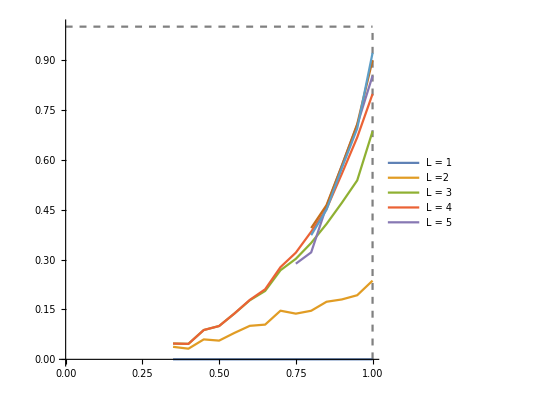

```mathematica
bestT =Table[Last@Transpose[ByLength[[i]]], {i, 1, Length@ByLength}];
visibility = Table[Transpose[ByLength[[i]]][[2]], {i, 1, Length@ByLength}];
plotPoints = Table[Transpose@{visibility[[i]], bestT[[i]]}, {i, 1, Length@visibility}];
plots = Show[ParametricPlot[{x,1}, {x,0,1}, PlotStyle->{Gray,Dashed}],ParametricPlot[{1,y}, {y,0,1}, PlotStyle->{Gray,Dashed}],ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 1", "L =2", "L = 3", "L = 4", "L = 5"},{0.6,0.7}], AxesLabel->{"visibility", "t"}], PlotRange->Full]
```

```mathematica
Export[path<>"figures/plot13-07-2021.png", plots, "PNG", RasterSize-> 2000];
```